# NG^23 T_11.Архитектура свёрточных нейронных сетей

Ковалевская Варвара
13-апр-2023

## Советы и подсказки

### Subsection. Загрузка базы растров MNIST

В каталоге  MNIST (см.[1]) приведены растры 28×28 рукописных цифр “0”–“9”.  База данных каталога находится в файлах: “train-images.idx3-ubyte”, “train-labels.idx1-ubyte” — 60 000 образцов тренировочного набора (Train) и “t10k-images.idx3-ubyte”, “t10k-labels.idx1-ubyte” — 10 000 образцов тестового набора (Test). Сами файлы и описание их структуры можно найти на сайте http://yann.lecun.com/exdb/mnist/index.html.

```mathematica
SetDirectory@NotebookDirectory[];
```

#### Subsection.Subsubsection. Загрузка набора растров ИмяНабора↦{Цифры,Растры}

```mathematica
ClearAll[LoadMNIST];
LoadMNIST[SetName_String]:=Module[{F,FDummy,Counter,Rows,Cols,Digits,Images},
F=OpenRead[ToLowerCase[SetName]<>"-images.idx3-ubyte",BinaryFormat->True];
{FDummy,Counter,Rows,Cols}=BinaryRead[F,Array["Integer32"&,4],ByteOrdering->+1];
Images=Fold[Partition[#,#2]&,BinaryReadList[F,"Byte",ByteOrdering->+1],{Cols,Rows}]/255.;
Close[F];
F=OpenRead[ToLowerCase[SetName]<>"-labels.idx1-ubyte",BinaryFormat->True];
{FDummy,Counter}=BinaryRead[F,Array["Integer32"&,2],ByteOrdering->+1];
Digits=BinaryReadList[F,"Byte",ByteOrdering->+1];
Close[F];
{Digits,Images}]
```

#### Subsection.Subsubsection. Загрузка тренировочных шаблонов TrainLabel→TrainImage

```mathematica
Map[Dimensions,Train=LoadMNIST["MNIST//train"]]
```

{{60000},{60000,28,28}}

#### Subsection.Subsubsection. Загрузка проверочных шаблонов TestLabel→TestImage

```mathematica
Map[Dimensions,Test=LoadMNIST["MNIST\\t10k"]]
```

{{10000},{10000,28,28}}

#### Subsection.Subsubsection. Загруженные наборы шаблонов

```mathematica
DynamicModule[{m=4},Grid[{
{Row@{"Magnification: ",SetterBar[Dynamic@m,Range[10]]},SpanFromLeft},{
Manipulate[Style[Train⟦1,n⟧,Bold,24+2m]->Image[Partition[256-Train⟦2,n⟧,28],"Byte",ColorSpace->"GrayScale",Magnification->m],{{n,37267,"Train"},1,Length@Train⟦1⟧,1,Appearance->"Labeled"},Paneled->False],
Manipulate[Style[Test⟦1,n⟧,Bold,24+2m]->Image[Partition[256-Test⟦2,n⟧,28],"Byte",ColorSpace->"GrayScale",Magnification->m],{{n,4655,"Test"},1,Length@Test⟦1⟧,1,Appearance->"Labeled"},Paneled->False]}},Frame->All,FrameStyle->Gray]]
```

Image::imgcsmis: The specified color space GrayScale and the number of channels 28 are not compatible.

## Советы и подсказки

## Section. Извлечение признаков

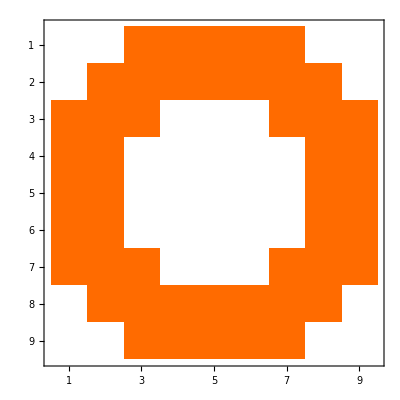

```mathematica
MatrixPlot[mask1 = DiskMatrix[4,9]-DiskMatrix[2,9]]
```

```mathematica
ListPlot3D[mask1,InterpolationOrder->1,ColorFunction->"TemperatureMap"]
```

-Graphics3D-

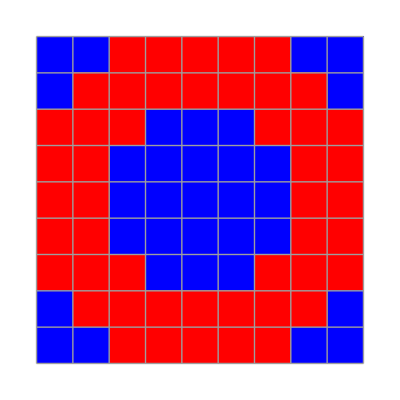

```mathematica
ArrayPlot[mask1,ColorFunction->(If[#1==0,Blue,Red]&),Mesh->True]
```

```mathematica
ColorFunction->(If[#1,Red,Blue]&)
```

```mathematica
pos6 = Flatten@RandomSample[Position[Train[[1]],6],4]
pos8 = Flatten@RandomSample[Position[Train[[1]],8],4]
pos9 = Flatten@RandomSample[Position[Train[[1]],9],4]
```

{59908,31517,36196,48302}

{58234,9971,31612,11507}

{36482,52479,442,37765}

```mathematica
Dimensions/@{Train[[2,pos6[[1]]]],mask1}
```

{{28,28},{9,9}}

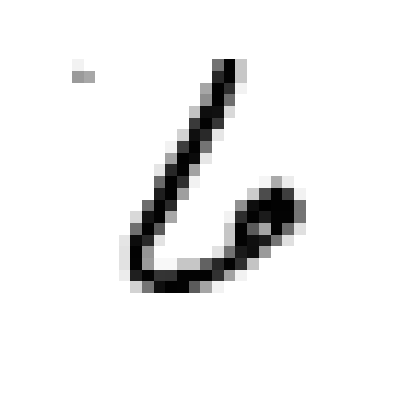
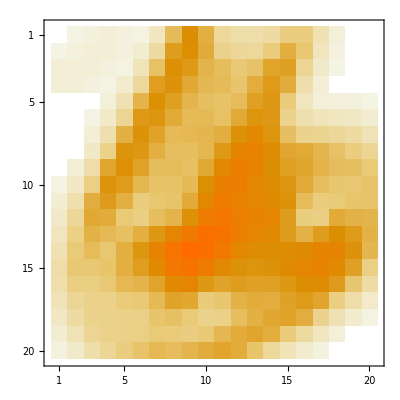
-Graphics-→-Graphics-

```mathematica
Train[[2,pos6[[1]]]];
ArrayPlot[%]->MatrixPlot[ListConvolve[mask1,%]]
```

## Section. Свёрточный слой

### Section.Subsection. Подслой свёртки

```mathematica
kmWeight1={First@#,ArrayReshape[Rest@#,{5,5}]}&/@RandomReal[{-1,1},{6,26}];
Map[Dimensions,%,{2}]
```

{{{},{5,5}},{{},{5,5}},{{},{5,5}},{{},{5,5}},{{},{5,5}},{{},{5,5}}}

```mathematica
ClearAll[kmConvolutionLayer1];
kmConvolutionLayer1 = Function[X,#1+ListConvolve[#2,X]&@@@kmWeight1]
```

Function[X,Apply[#1+ListConvolve[#2,X]&,kmWeight1,{1}]]

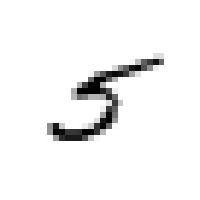
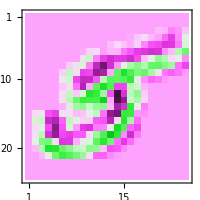
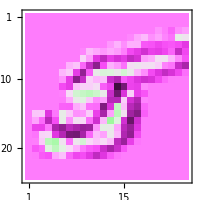
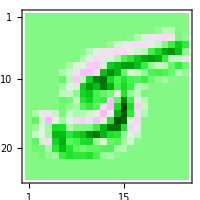
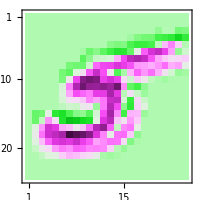
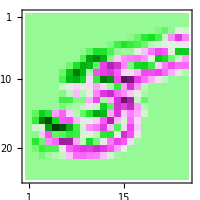
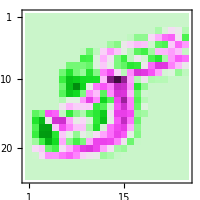
-Graphics-→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
RandomChoice@Train[[2]];
ArrayPlot[%,ImageSize->200]->Map[
MatrixPlot[#,ColorFunction->"GreenPinkTones",ImageSize->200]&,kmConvolutionLayer1@%]
```

### Section.Subsection. Подслой активации

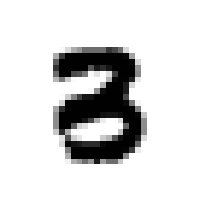

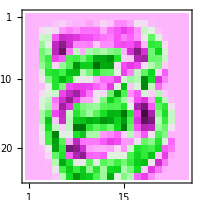
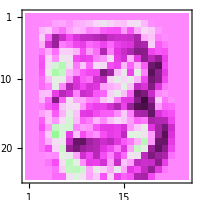
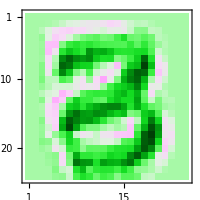
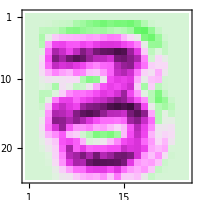
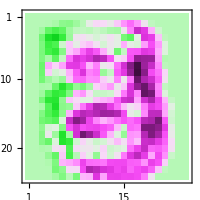
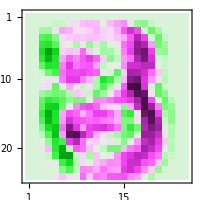

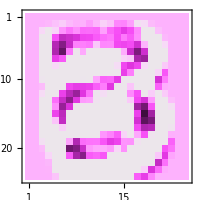

```mathematica
$=RandomChoice@Train[[2]];
ArrayPlot[$,ImageSize->200]
Map[MatrixPlot[#,ColorFunction->"GreenPinkTones",ImageSize->200]&,$11=kmConvolutionLayer1@$]
Map[MatrixPlot[#,ColorFunction->"GreenPinkTones",ImageSize->200]&,$12=Ramp@$11]
```

### Section.Subsection. Подслой подвыборки

```mathematica
$12//Dimensions
Dimensions[$13=Partition[#,{2,2}]&/@$12]
Dimensions[Map[Max,$13,{3}]]
```

{6,24,24}

{6,12,12,2,2}

{6,12,12}

```mathematica
ClearAll[kmPoolingLayer];
kmPoolingLayer = Function[X,Map[
Map[Max,Partition[#,{2,2}],{2}]&,
X]];
```

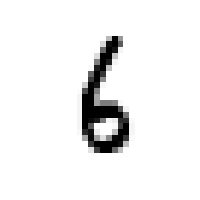

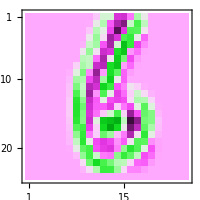
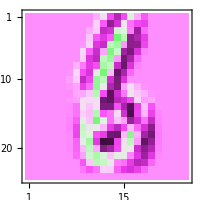
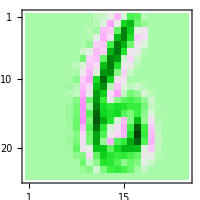
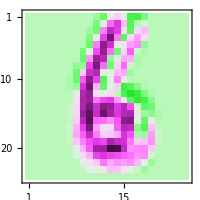
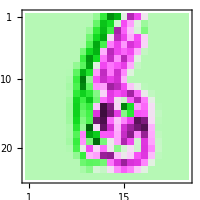
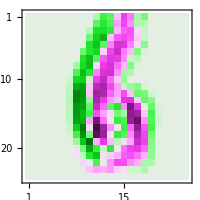

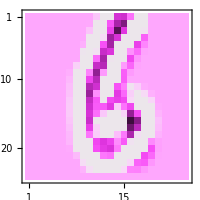

```mathematica
$=RandomChoice@Train[[2]];
ArrayPlot[$,ImageSize->200]
Map[MatrixPlot[#,ColorFunction->"GreenPinkTones",ImageSize->200]&,$11=kmConvolutionLayer1@$]
Map[MatrixPlot[#,ColorFunction->"GreenPinkTones",ImageSize->200]&,$12=Ramp@$11]
Map[MatrixPlot[#,ColorFunction->"GreenPinkTones",ImageSize->200]&,$13=kmPoolingLayer@$12]
```

## Section. Многоканальные изображения

### Section.Subsection. Подслой свёртки

```mathematica
kmWeight2={First@#,ArrayReshape[Rest@#,{6,6,6}]}&/@RandomReal[{-1,1},{10,217}];
Map[Dimensions,%,{2}]
Count[kmWeight2,_Real,∞]
```

{{{},{6,6,6}},{{},{6,6,6}},{{},{6,6,6}},{{},{6,6,6}},{{},{6,6,6}},{{},{6,6,6}},{{},{6,6,6}},{{},{6,6,6}},{{},{6,6,6}},{{},{6,6,6}}}

2170

```mathematica
kmWeight2[[1,2]]
ListConvolve[%,$13];
%//Dimensions
%%[[1,;; ;; 2,;; ;; 2]]//Dimensions
```

{{{-0.239422,0.102427,0.223064,0.759344,0.993158,-0.186573},{0.965313,-0.133589,0.0946209,0.686661,0.479892,-0.662332},{0.787651,0.0294576,-0.0746422,-0.599805,0.879558,-0.989379},{-0.434996,-0.778682,-0.419203,0.986741,-0.124234,0.0402161},{-0.896397,-0.556069,-0.717072,-0.550953,0.752284,0.737976},{-0.303226,0.49564,0.458348,-0.867498,0.554604,-0.654784}},{{-0.669966,0.451946,-0.412944,0.768904,-0.86492,-0.0838844},{0.204558,-0.775618,0.478179,-0.994351,-0.379039,-0.350096},{0.366472,0.397887,-0.109791,0.203309,0.0258274,-0.375057},{-0.445867,0.841078,-0.249659,-0.44055,-0.695968,-0.581708},{0.142435,0.562617,-0.530878,0.0773617,0.693454,0.29901},{-0.957098,0.975607,0.224833,0.951084,0.813262,0.17445}},{{0.0137177,-0.512647,-0.472837,0.737736,0.159584,0.261547},{0.105798,-0.361409,0.401123,0.18573,-0.382227,-0.766903},{-0.828209,0.64504,-0.422692,0.03553,-0.409049,0.669343},{-0.943969,0.936593,0.797919,0.453988,-0.754019,-0.643672},{0.377428,-0.474154,0.92818,0.709886,0.944409,0.778304},{-0.444191,-0.116514,0.41846,-0.791852,-0.447278,-0.851718}},{{0.639467,-0.269327,0.151931,-0.912325,-0.233391,0.499986},{-0.740994,0.748132,0.206182,-0.659056,0.564809,0.496109},{-0.393837,-0.665681,-0.284517,-0.276525,0.687497,-0.494698},{-0.439013,-0.240542,-0.970008,-0.267534,0.7299,0.13048},{0.986355,0.681457,0.551233,-0.696276,-0.874446,0.651719},{0.712249,-0.743378,0.267609,0.703881,-0.00490129,0.907999}},{{-0.0653809,-0.481345,0.495777,0.00301657,0.478021,-0.583933},{0.580167,-0.261713,0.878421,0.357922,-0.957778,-0.34739},{-0.0961316,-0.644542,-0.990296,0.437066,-0.636452,-0.993151},{0.219886,0.913374,-0.975285,0.526955,-0.475241,0.499559},{0.183898,-0.696356,-0.507303,-0.710472,-0.920405,-0.346589},{-0.306691,0.59085,0.00738304,-0.573844,-0.86369,-0.95499}},{{0.496569,-0.593011,-0.524752,0.490038,0.892547,0.730543},{0.850759,0.581746,0.725364,0.766496,0.335709,0.567066},{-0.701722,0.705028,0.207479,-0.687966,-0.611165,-0.384328},{0.425629,-0.00958547,0.854219,-0.363087,-0.902709,-0.139978},{-0.718081,0.485879,-0.572804,-0.312085,-0.242778,0.737018},{-0.170902,0.0597249,-0.579467,-0.254826,-0.563942,0.65605}}}

{1,7,7}

{4,4}

```mathematica
ClearAll[kmConvolutionLayer2];
kmConvolutionLayer2 = Function[X,#1+ListConvolve[#2,X][[1,;;;;2,;;;;2]]&@@@kmWeight2]
```

Function[X,Apply[#1+ListConvolve[#2,X]⟦1,1;;All;;2,1;;All;;2⟧&,kmWeight2,{1}]]

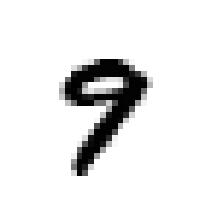

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
$=RandomChoice@Train[[2]];
ArrayPlot[$,ImageSize->200]
Map[MatrixPlot[#,ColorFunction->"GreenPinkTones",ImageSize->80]&,$11=$//kmConvolutionLayer1//Ramp//kmPoolingLayer]
Map[MatrixPlot[#,ColorFunction->"GreenPinkTones",ImageSize->80]&,$21=$11//kmConvolutionLayer2]
```

### Section.Subsection. Подслои активации и подвыборки

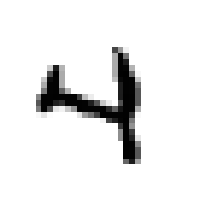

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
$=RandomChoice@Train[[2]];
ArrayPlot[$,ImageSize->200]
Map[MatrixPlot[#,ColorFunction->"GreenPinkTones",ImageSize->80]&,$11=$//kmConvolutionLayer1//Ramp//kmPoolingLayer]
Map[MatrixPlot[#,ColorFunction->"GreenPinkTones",ImageSize->80]&,$21=$11//kmConvolutionLayer2//Ramp//kmPoolingLayer]
```

## Section. Полносвязный слой

```mathematica
kmWeight3={First@#,Rest@#}&/@RandomReal[{-1,1},{50,41}];
Map[Dimensions,%]
Count[kmWeight3,_Real,∞]
```

{{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2}}

2050

```mathematica
$21//Dimensions
Flatten@$21;
#1+#2.%&@@@kmWeight3
```

{10,2,2}

{14.6405,19.9986,16.9497,-42.4477,-53.6239,-22.1682,24.6228,10.5456,-14.2122,106.039,-22.3897,-5.65476,52.2448,-56.8255,-15.0334,40.4031,-13.0354,57.7035,-11.0148,47.4589,54.5901,-60.9112,3.40704,-13.1502,-30.3568,83.8548,14.3003,37.9618,-6.49878,-17.4085,54.6574,93.3002,5.87432,-6.02095,18.146,-3.74678,-9.92476,-93.0354,21.54,42.5195,-6.68088,5.41294,54.3366,-25.4507,-10.6773,54.8593,83.631,-35.5193,-32.1545,-71.045}

```mathematica
ClearAll[kmFullyConnectedLayer3,LReLU];
LReLU=If[#<0,0.01 #,#]&
kmFullyConnectedLayer3 = Function[X,Block[{x=Flatten@X},#1+#2.x&@@@kmWeight3]]
```

If[#1<0,0.01 #1,#1]&

Function[X,Block[{x=Flatten[X]},Apply[#1+#2.x&,kmWeight3,{1}]]]

```mathematica
$21//kmFullyConnectedLayer3
```

{14.6405,19.9986,16.9497,-42.4477,-53.6239,-22.1682,24.6228,10.5456,-14.2122,106.039,-22.3897,-5.65476,52.2448,-56.8255,-15.0334,40.4031,-13.0354,57.7035,-11.0148,47.4589,54.5901,-60.9112,3.40704,-13.1502,-30.3568,83.8548,14.3003,37.9618,-6.49878,-17.4085,54.6574,93.3002,5.87432,-6.02095,18.146,-3.74678,-9.92476,-93.0354,21.54,42.5195,-6.68088,5.41294,54.3366,-25.4507,-10.6773,54.8593,83.631,-35.5193,-32.1545,-71.045}

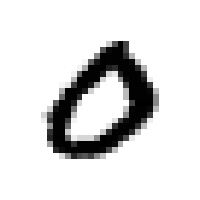

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

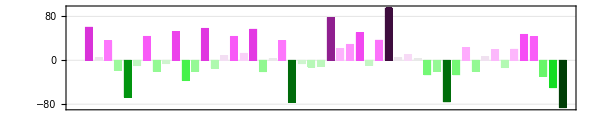

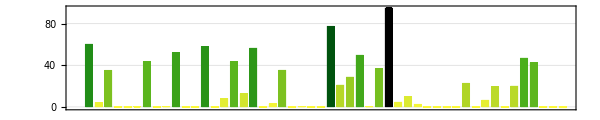

```mathematica
$=RandomChoice@Train[[2]];
ArrayPlot[$,ImageSize->200]
Map[MatrixPlot[#,ColorFunction->"GreenPinkTones",ImageSize->80]&,$1=$//kmConvolutionLayer1//Ramp//kmPoolingLayer]
Map[MatrixPlot[#,ColorFunction->"GreenPinkTones",ImageSize->80]&,$2=$1//kmConvolutionLayer2//Ramp//kmPoolingLayer]
BarChart[$3=kmFullyConnectedLayer3@$2,ColorFunction->"GreenPinkTones",AspectRatio->.2,ImageSize->600,Frame->True,GridLines->Automatic]
BarChart[$4=LReLU/@$3,ColorFunction->ColorData[{"AvocadoColors","Reverse"}],AspectRatio->.2,ImageSize->600,Frame->True,GridLines->Automatic]
```

## Section. Выходной слой с функцией активации SoftMax

```mathematica
SoftMax=SoftmaxLayer["Input"->10]
```

SoftmaxLayer[<>]

```mathematica
%295@$4
Total/@{$4,%}
```

```mathematica
kmWeight4={First@#,Rest@#}&/@RandomReal[{-1,1},{10,51}];
Map[Dimensions,%]
Count[kmWeight3,_Real,∞]
```

{{2},{2},{2},{2},{2},{2},{2},{2},{2},{2}}

2050

```mathematica
ClearAll[kmFullyConnectedLayer3,LReLU];
LReLU=If[#<0,0.01 #,#]&
kmFullyConnectedLayer3 = Function[X,Block[{x=Flatten@X},#1+#2.x&@@@kmWeight3]]
```

If[#1<0,0.01 #1,#1]&

Function[X,Block[{x=Flatten[X]},Apply[#1+#2.x&,kmWeight3,{1}]]]

```mathematica
ClearAll[kmFullyConnectedLayer4,LReLU];
LReLU=If[#<0,0.01 #,#]&
kmFullyConnectedLayer4 = Function[X,Block[{x=Flatten@X},#1+#2.x&@@@kmWeight4]]
```

If[#1<0,0.01 #1,#1]&

Function[X,Block[{x=Flatten[X]},Apply[#1+#2.x&,kmWeight4,{1}]]]

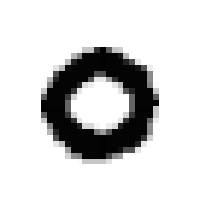

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

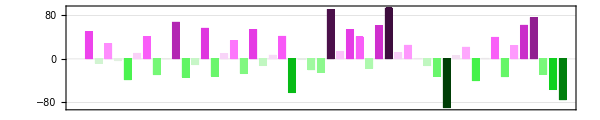

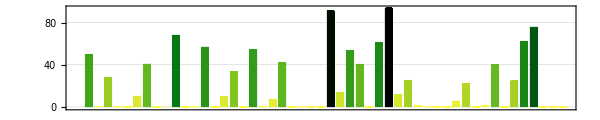

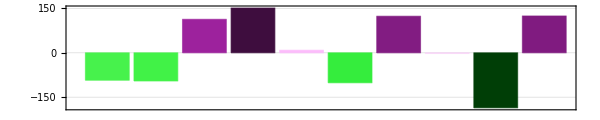

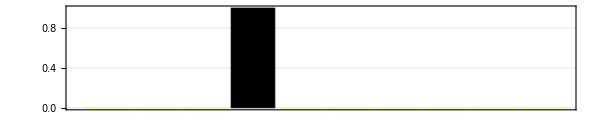

```mathematica
$=RandomChoice@Train[[2]];
ArrayPlot[$,ImageSize->200]
Map[MatrixPlot[#,ColorFunction->"GreenPinkTones",ImageSize->80]&,$1=$//kmConvolutionLayer1//Ramp//kmPoolingLayer]
Map[MatrixPlot[#,ColorFunction->"GreenPinkTones",ImageSize->80]&,$2=$1//kmConvolutionLayer2//Ramp//kmPoolingLayer]
BarChart[$31=kmFullyConnectedLayer3@$2,ColorFunction->"GreenPinkTones",AspectRatio->.2,ImageSize->600,Frame->True,GridLines->Automatic]
BarChart[$32=LReLU/@$31,ColorFunction->ColorData[{"AvocadoColors","Reverse"}],AspectRatio->.2,ImageSize->600,Frame->True,GridLines->Automatic]
BarChart[$41 =kmFullyConnectedLayer4@$32,ColorFunction->"GreenPinkTones",AspectRatio->.2,ImageSize->600,Frame->True,GridLines->Automatic]
BarChart[$42=SoftMax[$41],ColorFunction->ColorData[{"AvocadoColors","Reverse"}],AspectRatio->.2,ImageSize->600,Frame->True,GridLines->Automatic]
```

## Section. Свёрточная нейронная сеть

```mathematica
kmCNN[X_]:=X//kmConvolutionLayer1//Ramp//kmPoolingLayer//
kmConvolutionLayer2//Ramp//kmPoolingLayer//
kmFullyConnectedLayer3//Map[LReLU]//
kmFullyConnectedLayer4//SoftMax;
```